```mathematica
d=Import["/home/data/promotion/Programmierung/fipster/output/Decisions/newest/Decisions1-grid1-40000000.dat"][[4;;]];
```

```mathematica
delta[i_,n_]:=((a^2-b^2) f[x]+b^2 f[a+x]-a^2 f[-b+x])/(a b (a+b))/.{f[x]-> d[[i,n]],f[x+a]-> d[[i+1,n]],f[-b+x]->d[[i-1,n]]
,a-> d[[i+1,1]]-d[[i,1]],b-> d[[i,1]]-d[[i-1,1]]}
```

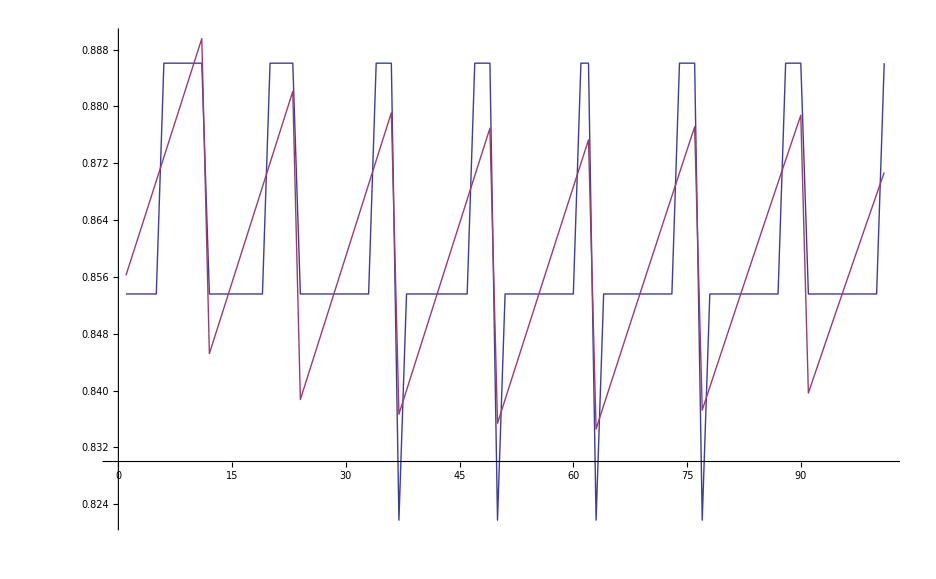

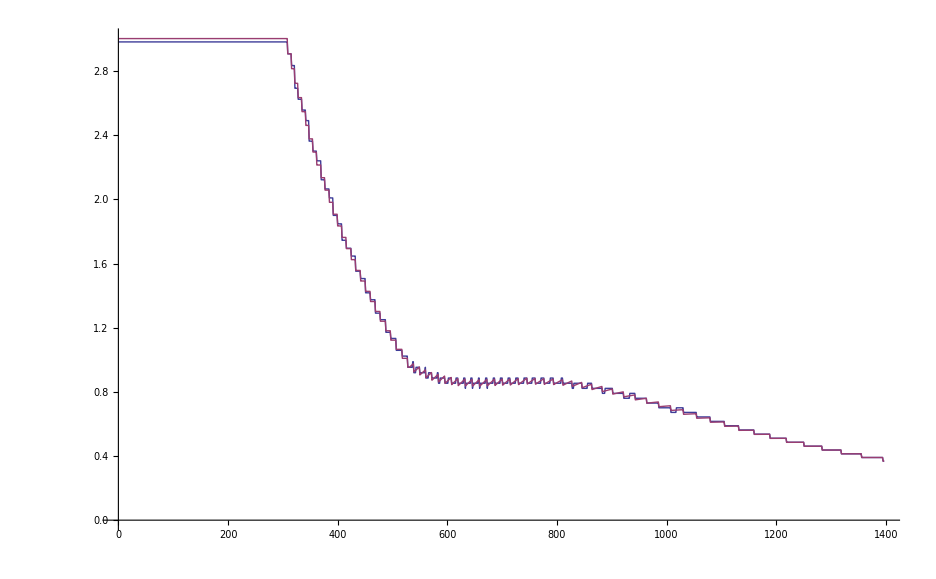

```mathematica
h[i_]:=Transpose[d][[i]];
a1=600;a2=700;
ListLinePlot[{h[6][[a1;;a2]],h[9][[a1;;a2]]+Table[delta[i,2],{i,a1,a2}]}]
a1=4;a2=1400;
ListLinePlot[{h[6][[a1;;a2]],h[9][[a1;;a2]]+Table[delta[i,2],{i,a1,a2}]}]
```

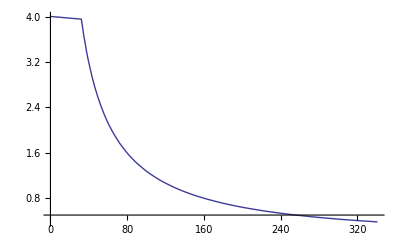

```mathematica
s[i_]:=h[i][[2;;1400]];
ds=Differences[Prepend[s[9],0]];
res=Pick[Transpose[{s[1],Prepend[
MovingAverage[s[9],2],s[9][[1]]]
}],#!=0.&/@ds];
ListLinePlot[res,PlotRange->All]
```

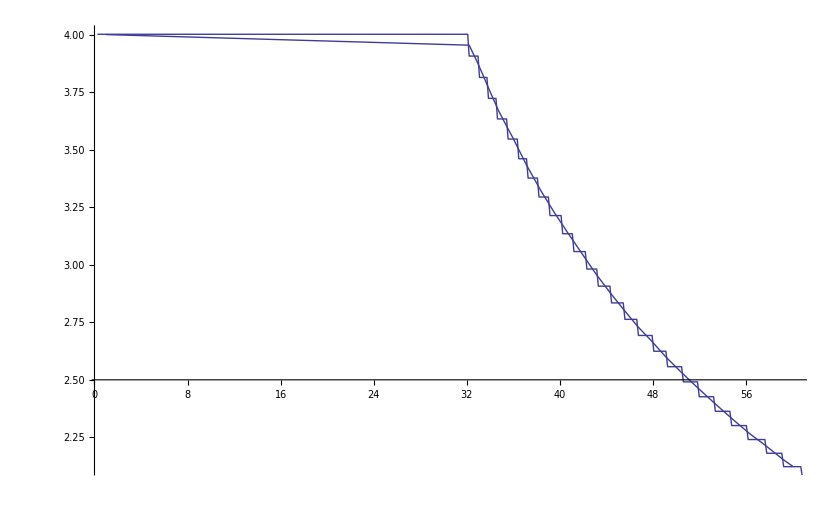

```mathematica
f=Interpolation[res,InterpolationOrder->1];
Show[Plot[f[x],{x,1,60}],ListLinePlot[Transpose[{h[1],h[9]}][[a1;;a2]]]]
```

InterpolatingFunction::dmval: Input value {341.679} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {342.218} lies outside the range of data in the interpolating function. Extrapolation will be used.

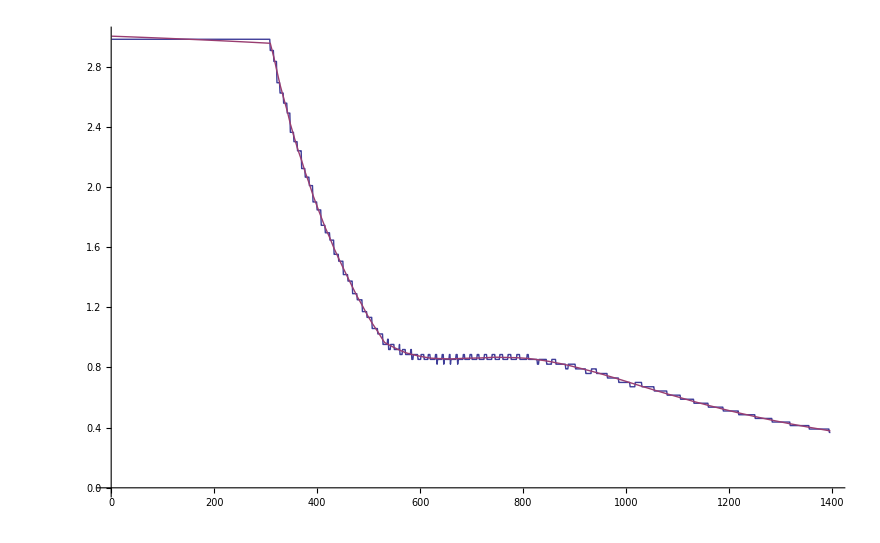

```mathematica
ListLinePlot[{h[6][[a1;;a2]],Table[f[h[1][[i]]]+delta[i,2],{i,a1,a2}]}]
```